# Cardiod Arc-en-Ciel

June 20, 2020

Copyright (c) David M. Morgan, Ph.D.
GNU General Public License, v. 3.0 or later
Antigonish Landing, NS B2G 2L2 Canada
dmmorgan@gmail.com

Algorithm:

From:

http://mathworld.wolfram.com/Cardioid.html

The cardioid may also be generated as follows. Draw a circle C and fix a point A on it. Now draw a set of circles centered on the 	circumference of C and passing through A. The envelope of these circles is then a cardioid (Pedoe 1995).

Code:

Define the circle C and an arbitrary point A:

```mathematica
CircleCPoints = Table[
{Cos[2 Pi i / 39], Sin[2 Pi i / 39]},
{i, 1, 39}
]

PointA = {0,1}
```

{{Cos[(2 π)/39],Sin[(2 π)/39]},{Cos[(4 π)/39],Sin[(4 π)/39]},{Cos[(2 π)/13],Sin[(2 π)/13]},{Cos[(8 π)/39],Sin[(8 π)/39]},{Sin[(19 π)/78],Cos[(19 π)/78]},{Sin[(5 π)/26],Cos[(5 π)/26]},{Sin[(11 π)/78],Cos[(11 π)/78]},{Sin[(7 π)/78],Cos[(7 π)/78]},{Sin[π/26],Cos[π/26]},{-Sin[π/78],Cos[π/78]},{-Sin[(5 π)/78],Cos[(5 π)/78]},{-Sin[(3 π)/26],Cos[(3 π)/26]},{-1/2,(√3)/2},{-Sin[(17 π)/78],Cos[(17 π)/78]},{-Cos[(3 π)/13],Sin[(3 π)/13]},{-Cos[(7 π)/39],Sin[(7 π)/39]},{-Cos[(5 π)/39],Sin[(5 π)/39]},{-Cos[π/13],Sin[π/13]},{-Cos[π/39],Sin[π/39]},{-Cos[π/39],-Sin[π/39]},{-Cos[π/13],-Sin[π/13]},{-Cos[(5 π)/39],-Sin[(5 π)/39]},{-Cos[(7 π)/39],-Sin[(7 π)/39]},{-Cos[(3 π)/13],-Sin[(3 π)/13]},{-Sin[(17 π)/78],-Cos[(17 π)/78]},{-1/2,-(√3)/2},{-Sin[(3 π)/26],-Cos[(3 π)/26]},{-Sin[(5 π)/78],-Cos[(5 π)/78]},{-Sin[π/78],-Cos[π/78]},{Sin[π/26],-Cos[π/26]},{Sin[(7 π)/78],-Cos[(7 π)/78]},{Sin[(11 π)/78],-Cos[(11 π)/78]},{Sin[(5 π)/26],-Cos[(5 π)/26]},{Sin[(19 π)/78],-Cos[(19 π)/78]},{Cos[(8 π)/39],-Sin[(8 π)/39]},{Cos[(2 π)/13],-Sin[(2 π)/13]},{Cos[(4 π)/39],-Sin[(4 π)/39]},{Cos[(2 π)/39],-Sin[(2 π)/39]},{1,0}}

{0,1}

For each point in CircleCPoints, construct a circle with that point as its centre such that it passes through A. In other words, each such circle must satisfy:

r^2=(x-CircleCPoints[[i,1]])^2+ (y-CircleCPoints[[i,2]])^2

in which x and y take on the values of PointA[[1]] and PointA[[2]], respectively, and in which 

r

is the radius of the circle in question. 

For each point in CircleCPoints, the radius of the required circle is:

```mathematica
ConstructedCircleRadii = Table[
Sqrt[(PointA[[1]] - CircleCPoints[[i,1]])^2 + (PointA[[2]] - CircleCPoints[[i,2]])^2],
{i, Length[CircleCPoints]}
];
```

Give the third result as an example:

```mathematica
ConstructedCircleRadii[[3]]
```

√(Cos[(2 π)/13]^2+(1-Sin[(2 π)/13])^2)

Formulate the equation for the upper hemisphere of each to be constructed circle in the form: 

y = f(x)

Recalling that each circle satisfies:

r^2=(x-CircleCPoints[[i,1]])^2+ (y-CircleCPoints[[i,2]])^2,     (1)

one rearranges to solve for y: 

r^2 - (x-CircleCPoints[[i,1]])^2 = (y-CircleCPoints[[i,2]])^2.     (2)

Taking square roots of each side provides:

.03√(.16 r^2-(x-CircleCPoints[[i,1]])^2) = (y-CircleCPoints[[i,2]]),     (3)

and solving for y gives:

y = CircleCPoints[[i,2]] + √(.16 r^2-(x-CircleCPoints[[i,1]])^2).    (4)

Construct the equations for the upper hemisphere of each circle:

```mathematica
UpperHemisphereEquations = Table[
CircleCPoints[[i,2]] + Sqrt[
ConstructedCircleRadii[[i]]^2 - 
(x - CircleCPoints[[i,1]])^2
],
{i, Length[CircleCPoints]}
];
```

Give the third result as an example.

```mathematica
UpperHemisphereEquations[[3]]
```

√(-(x-Cos[(2 π)/13])^2+Cos[(2 π)/13]^2+(1-Sin[(2 π)/13])^2)+Sin[(2 π)/13]

Plot each upper hemisphere. Note the color formula in PlotStyle. Show the third in the list as an example.

```mathematica
UpperHemispherePlots = Table[
Plot[
UpperHemisphereEquations[[i]],
{
x, 
-ConstructedCircleRadii[[i]] + CircleCPoints[[i,1]],
ConstructedCircleRadii[[i]] + CircleCPoints[[i,1]]
},
ColorFunction ->(ColorData["Rainbow"][Rescale[#1,{-3, 3}]]&),
ColorFunctionScaling -> False,
PlotRange -> {{-3,3},{-3,3}}
],
{i, Length[ConstructedCircleRadii]}
];
```

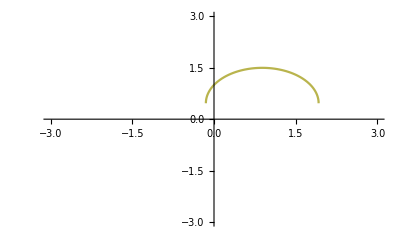

```mathematica
UpperHemispherePlots[[3]]
```

Construct the equations for the lower hemisphere of each circle:

Recalling that each circle satisfies:

r^2=(x-CircleCPoints[[i,1]])^2+ (y-CircleCPoints[[i,2]])^2,     (1)

one rearranges to solve for y: 

r^2 - (x-CircleCPoints[[i,1]])^2 = (y-CircleCPoints[[i,2]])^2.     (2)

Taking square roots of each side, and, this time, taking the negative root of the right hand side,  provides:

.03√(.16 r^2-(x-CircleCPoints[[i,1]])^2) = - (y-CircleCPoints[[i,2]]),     (5)

and solving for y gives:

y = CircleCPoints[[i,2]] - √(.16 r^2-(x-CircleCPoints[[i,1]])^2).    (6)

```mathematica
LowerHemisphereEquations = Table[
CircleCPoints[[i,2]] - 
Sqrt[
ConstructedCircleRadii[[i]]^2 - 
(x - CircleCPoints[[i,1]])^2
],
{i, Length[CircleCPoints]}
];
```

Plot each lower hemisphere. Show the third in the list as an example.

```mathematica
LowerHemispherePlots = Table[
Plot[
LowerHemisphereEquations[[i]],
{
x, 
-ConstructedCircleRadii[[i]] + CircleCPoints[[i,1]],
ConstructedCircleRadii[[i]] + CircleCPoints[[i,1]]
},
ColorFunction ->(ColorData["Rainbow"][Rescale[#2,{-3, 1}]]&),
ColorFunctionScaling -> False,
PlotRange -> {{-3,3},{-3,3}}
],
{i, Length[ConstructedCircleRadii]}
];
```

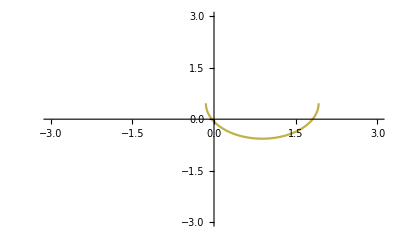

```mathematica
LowerHemispherePlots[[3]]
```

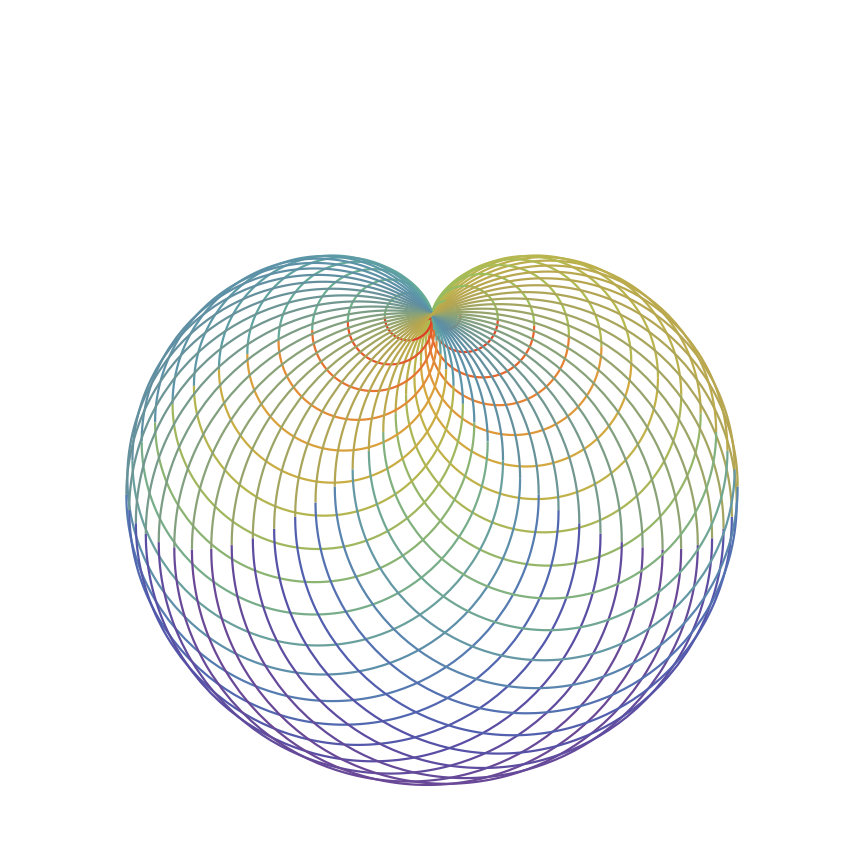

2LU2D 1UL2R.jpg

```mathematica
ConstructedCirclePlots = 
Table[
Show[
UpperHemispherePlots[[i]],
LowerHemispherePlots[[i]],
AspectRatio -> 1
],
{i, Length[UpperHemispherePlots]}
];

CardiodPlot = Show[
Table[
ConstructedCirclePlots[[i]],
{i, Length[ConstructedCirclePlots]}
],
Axes -> False,
ImageSize -> {12 72, 12 72}
]

Export["2LU2D 1UL2R.jpg",
 CardiodPlot]
```

VisibleSpectrum!!